```mathematica
Off[General::munfl]
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/AcoreNteraction/source_mathematica

```mathematica
lecs={{0.25,0.0036,-30.9795},{1.00,0.0036,-117.5248},{2.25,0.0036,-259.7207},{4.00,0.0036,-457.5555},{6.25,0.0036,-711.0607},{9.00,0.0036,-1020.1831},{12.25,0.0036,-1385.0069},{16.00,0.0036,-1805.4404},{20.25,0.0036,-2281.5596},{25.00,0.0036,-2813.2897}};
lecnbr=Length[lecs];
```

## Finite differences

```mathematica
SolveSecular[Ene_?NumberQ, Rdis_?NumberQ,Npoints_?NumberQ,mh2_?NumberQ,Local_:False,V0_,W_,α_,λ_,C0_]:=Block[{e,Rmax,nGrid,hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,asywf,wf,wffree,Tere,fit,nn,δ,L,r,mod,usol},
e=Ene;
Rmax=Rdis;
nGrid=Npoints;
hDif=Rmax/nGrid;
L=0;

(* Matrix components *)
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{nGrid,nGrid}];
Dmat=DiagonalMatrix[Table[hDif^2 mh2(e-V0[i hDif,α,λ,C0])+(L(L+1))/i^2,{i,1,nGrid}]];
If[Local≠True,
Wmat=Table[hDif^2 mh2 W[i hDif,j hDif, e,α,λ,C0],{i,1,nGrid},{j,1,nGrid}]; 
,
(*Print[">> ... Local approximation ..."];*)
Wmat=DiagonalMatrix[Table[hDif^2 mh2 W[i hDif,i hDif, e,α,λ,C0],{i,1,nGrid}]]; ];

If[e==0, 
bcol=Table[Which[i==nGrid,-hDif,1==1,0],{i,1,nGrid}];
Dmat⟦nGrid⟧⟦nGrid⟧+=1; (*this is only for 0 energy*)
,
bcol=Table[Which[i==nGrid,-1,1==1,0],{i,1,nGrid}];
];
ucol=Array[Subscript["u", ##]&,{nGrid}];
Amat=Dmat+Wmat+Kmat;


usol=LinearSolve[Amat,bcol];
wf=Table[{i hDif,usol⟦i⟧},{i,1,nGrid}];

If[e==0, 
wffree=Table[{i hDif,(usol[[-1]]-usol[[-2]]) i+usol[[-2]]-(usol[[-1]]-usol[[-2]]) nGrid},{i,1,nGrid}];
Tere=Rmax-usol⟦-1⟧;
,
asywf=nn Sin[Sqrt[mh2 e] r+δ];
fit=FindFit[wf,asywf,{nn,δ},r];
mod=Function[{r},Evaluate[asywf/.fit]];wffree=Table[{i hDif,mod[i hDif]},{i,1,nGrid}];
Tere=-(1/Sqrt[mh2 e]) Tan[δ/.fit[[2]]];
];
{Tere,wffree,wf}
]
```

### nucleon-nucleon EFT_nopi leading-order benchmark

μ = 469.46 MeV    hbarc = 197.327 MeV·fm    h^2/2μ = 41.471 MeV·fm^2

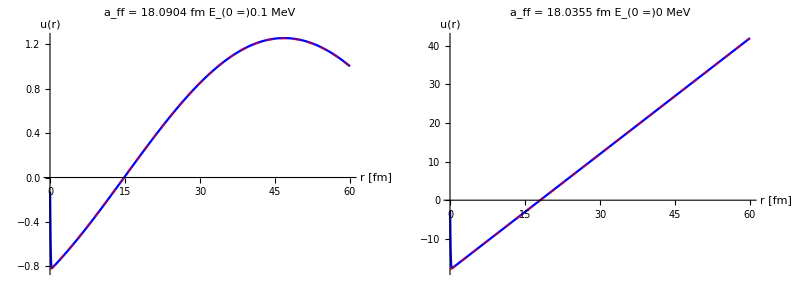

```mathematica
Rmax=60;nGrid=2500;
μ=938.92/2;hbar=197.327053;mh2=(2 μ)/(hbar)^2;e1=0.1;e2=0;
Print["μ = ", μ, " MeV    hbarc = ",hbar, " MeV·fm    h^2/2μ = ", N[1/mh2 ]," MeV·fm^2"];

Λ=lecs[[lecnbr]][[1]];λ=Λ;
C0=lecs[[lecnbr]][[3]];
V0[r_]:= C0 Exp[- λ r^2];
W[r_,rp_,e_]:=0;

nonzeroSOL=SolveSecular[e1,Rmax,nGrid,mh2,True,V0,W];
zeroSOL=SolveSecular[e2,Rmax,nGrid,mh2,True,V0,W];

Grid[{{
ListLinePlot[{nonzeroSOL[[3]],nonzeroSOL[[2]]},PlotStyle->{Blue,{Red,Opacity->0.5,Dashed}},AxesLabel->{"r [fm]","u(r)"},PlotRange->{Automatic,Automatic},PlotLabel->"a_ff = "<>ToString[nonzeroSOL[[1]]]<>" fm    E_(0 =)"<>ToString[e1]<>" MeV",ImageSize->Large],
ListLinePlot[{zeroSOL[[3]],zeroSOL[[2]]},PlotStyle->{Blue,{Red,Opacity->0.5,Dashed}},AxesLabel->{"r [fm]","u(r)"},PlotRange->{Automatic,Automatic},PlotLabel->"a_ff = "<>ToString[zeroSOL[[1]]]<>" fm    E_(0 =)"<>ToString[e2]<>" MeV",ImageSize->Large]}}]
```

```mathematica
affofL={};
Rmax=60;nGrid=2500;
μ=938.92/2;hbar=197.327053;mh2=(μ 2)/(hbar)^2;e0=0.0;
Do[
Λ=pot[[1]];λ=Λ;
C0=pot[[3]];
V0[r_]:= C0 Exp[-λ r^2];
W[r_,rp_,e_]:=0;
a0=SolveSecular[e0,Rmax,nGrid,mh2,True,V0,W][[1]];
AppendTo[affofL,{Λ,a0}];
Print["λ = ",N[λ,4]," fm^-2     C_0 = ",N[C0,4]," MeV     a_0 = ",N[a0,4]," fm"]
,{pot,lecs}]
ListPlot[affofL,AxesLabel->{"Λ [fm^-2]","a_ff [fm]"}]
```

λ = 0.25 fm^-2     C_0 = -30.9795 MeV     a_0 = 21.8387 fm

λ = 1. fm^-2     C_0 = -117.525 MeV     a_0 = 21.0723 fm

λ = 2.25 fm^-2     C_0 = -259.721 MeV     a_0 = 20.7748 fm

λ = 4. fm^-2     C_0 = -457.556 MeV     a_0 = 20.5714 fm

λ = 6.25 fm^-2     C_0 = -711.061 MeV     a_0 = 20.3192 fm

λ = 9. fm^-2     C_0 = -1020.18 MeV     a_0 = 20.0526 fm

λ = 12.25 fm^-2     C_0 = -1385.01 MeV     a_0 = 19.6587 fm

λ = 16. fm^-2     C_0 = -1805.44 MeV     a_0 = 19.2162 fm

λ = 20.25 fm^-2     C_0 = -2281.56 MeV     a_0 = 18.6582 fm

λ = 25. fm^-2     C_0 = -2813.29 MeV     a_0 = 18.0355 fm

```mathematica
a0
```

### (AB)-(AB) dimer-dimer EFT_nopi leading-order calculation

single-channel RGM in zero-energy, zero-range, and local-approximation

μ = 938.92     hbarc = 197.327     h^2/2μ = 20.7355

λ = 25.fm^-2     C_0 = -2813.29MeV    α = 0.0036fm^-2

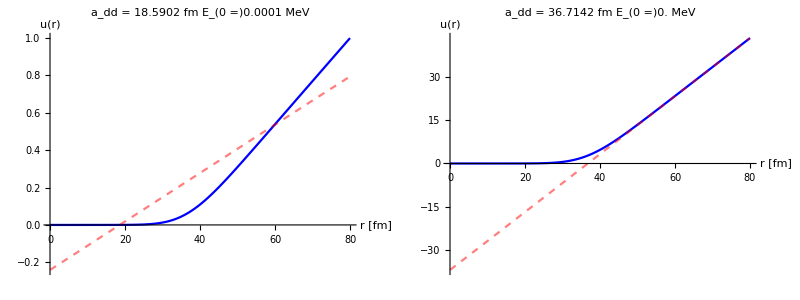

```mathematica
μ=938.92;mh2=(2 μ)/(hbar)^2;hbar=197.327053;Rmax=80;nGrid=2000;e1=0.0001;e2=0.0;

Λ=lecs[[lecnbr]][[1]];λ=Λ;
α=lecs[[lecnbr]][[2]];
C0=lecs[[lecnbr]][[3]];
Print["μ = ", μ, "     hbarc = ",hbar, "     h^2/2μ = ", N[1/mh2 ]];
Print["λ = ",λ,"fm^-2     C_0 = ",C0,"MeV    α = ",α,"fm^-2"];
(* eq.(23) OverHat[=] zero-range, zero-energy, and localized (ab)-(ab) potential *)
V0[r_]:=hbar^2/(2 μ) (4 α^2 r^2-2 α) 8 Pi^1.5 Exp[-α r^2]+C0 (2 α/(2 α+λ))^1.5 (2 Exp[-2 α r^2]-16 Pi^1.5 Exp[-3 α r^2]);
W[r_,rp_,e_]:=0;

nonzeroSOL=SolveSecular[e1,Rmax,nGrid,mh2,True,V0,W];
zeroSOL=SolveSecular[e2,Rmax,nGrid,mh2,True,V0,W];

Grid[{{
ListLinePlot[{nonzeroSOL[[3]],nonzeroSOL[[2]]},PlotStyle->{Blue,{Red,Opacity->0.5,Dashed}},AxesLabel->{"r [fm]","u(r)"},PlotRange->{Automatic,Automatic},PlotLabel->"a_dd = "<>ToString[nonzeroSOL[[1]]]<>" fm    E_(0 =)"<>ToString[e1]<>" MeV",ImageSize->Large],
ListLinePlot[{zeroSOL[[3]],zeroSOL[[2]]},PlotStyle->{Blue,{Red,Opacity->0.5,Dashed}},AxesLabel->{"r [fm]","u(r)"},PlotRange->{Automatic,Automatic},PlotLabel->"a_dd = "<>ToString[zeroSOL[[1]]]<>" fm    E_(0 =)"<>ToString[e2]<>" MeV",ImageSize->Large]}}]
```

Λ = 0.25 fm^-2     C_0 = -30.9795 MeV     a_0 = 36.7142 fm

Λ = 1. fm^-2     C_0 = -117.525 MeV     a_0 = 36.7142 fm

Λ = 2.25 fm^-2     C_0 = -259.721 MeV     a_0 = 36.7142 fm

Λ = 4. fm^-2     C_0 = -457.556 MeV     a_0 = 36.7142 fm

Λ = 6.25 fm^-2     C_0 = -711.061 MeV     a_0 = 36.7142 fm

Λ = 9. fm^-2     C_0 = -1020.18 MeV     a_0 = 36.7142 fm

Λ = 12.25 fm^-2     C_0 = -1385.01 MeV     a_0 = 36.7142 fm

Λ = 16. fm^-2     C_0 = -1805.44 MeV     a_0 = 36.7142 fm

Λ = 20.25 fm^-2     C_0 = -2281.56 MeV     a_0 = 36.7142 fm

Λ = 25. fm^-2     C_0 = -2813.29 MeV     a_0 = 36.7142 fm

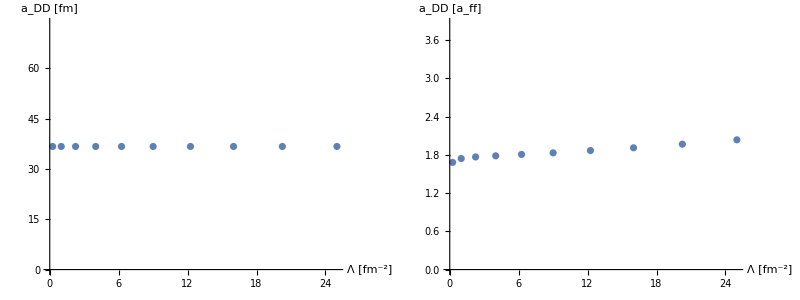

```mathematica
addofL={};μ=938.92;mh2=(2 μ)/(hbar)^2;e0=0.0;hbar=197.327053;
Do[
Λ=pot[[1]];λ=Λ;
C0=pot[[3]];α=pot[[2]];
V0[r_]:=hbar^2/(2 μ) (4 α^2 r^2-2 α) 8 Pi^1.5 Exp[-α r^2]+C0 (2 α/(2 α+λ))^1.5 (2 Exp[-2 α r^2]-16 Pi^1.5 Exp[-3 α r^2]);
W[r_,rp_,e_]:=0;
a0=SolveSecular[e0,Rmax,nGrid,mh2,True,V0,W][[1]];
AppendTo[addofL,{Λ,a0}];
Print["Λ = ",Λ," fm^-2     C_0 = ",C0," MeV     a_0 = ",a0," fm"]
,{pot,lecs}]
addbyaffofL=Table[{lecs[[n]][[1]],addofL[[n]][[2]]/affofL[[n]][[2]]},{n,Length[lecs]}];
Grid[{{ListPlot[addofL,AxesLabel->{"Λ [fm^-2]","a_DD [fm]"}],ListPlot[addbyaffofL,PlotRange->{Automatic,{0,2.1 Mean[addbyaffofL[[All,2]]]}},AxesLabel->{"Λ [fm^-2]","a_DD [a_ff]"}]}}]
```

single-channel RGM (non-local)

μ = 938.92     hbarc = 197.327     h^2/2μ = 20.7355

λ = 25.fm^-2     C_0 = -2813.29MeV    α = 0.0036fm^-2

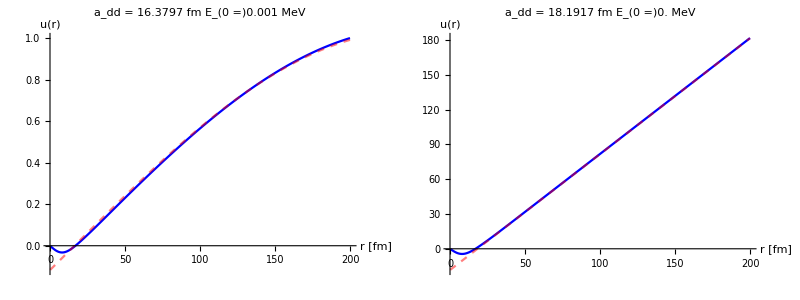

```mathematica
lecnbr=10;
μ=938.92;mh2=(2 μ)/(hbar)^2;hbar=197.327053;Rmax=200;nGrid=1600;e1=0.001;e2=0.0;

Λ=lecs[[lecnbr]][[1]];λ=Λ;
α=lecs[[lecnbr]][[2]];
C0=lecs[[lecnbr]][[3]];
Print["μ = ", μ, "     hbarc = ",hbar, "     h^2/2μ = ", N[1/mh2 ]];
Print["λ = ",λ,"fm^-2     C_0 = ",C0,"MeV    α = ",α,"fm^-2"];
(* eq.(21) *)
V0[r_,α_,λ_,C0_]:=C0 (2 α/(2 α+λ))^1.5 Exp[-2 α λ/(2 α+λ) r^2];
(* eq.(22) with partial-wave-projection coefficients *)
W[r_,rp_,e_,α_,λ_,C0_]:=(4π r rp) ( 8 α^(3/2)(hbar^2/(2 μ) (4 α^2 r^2-2 α)+e0)ⅇ^(-α(rp^2+r^2))-C0(2 α/(2 α+λ))^1.5 ⅇ^(-α(rp^2+(2α+3λ)/(2α+λ)r^2)));

nonzeroSOL=SolveSecular[e1,Rmax,nGrid,mh2,False,V0,W,α,λ,C0];
zeroSOL=SolveSecular[e2,Rmax,nGrid,mh2,False,V0,W,α,λ,C0];

Grid[{{
ListLinePlot[{nonzeroSOL[[3]],nonzeroSOL[[2]]},PlotStyle->{Blue,{Red,Opacity->0.5,Dashed}},AxesLabel->{"r [fm]","u(r)"},PlotRange->{Automatic,Automatic},PlotLabel->"a_dd = "<>ToString[nonzeroSOL[[1]]]<>" fm    E_(0 =)"<>ToString[e1]<>" MeV",ImageSize->Large],
ListLinePlot[{zeroSOL[[3]],zeroSOL[[2]]},PlotStyle->{Blue,{Red,Opacity->0.5,Dashed}},AxesLabel->{"r [fm]","u(r)"},PlotRange->{Automatic,Automatic},PlotLabel->"a_dd = "<>ToString[zeroSOL[[1]]]<>" fm    E_(0 =)"<>ToString[e2]<>" MeV",ImageSize->Large]}}]
```

```mathematica
addofLNL={};μ=938.92;mh2=(μ 2)/(hbar)^2;e0=0.00001;hbar=197.327053;
Rmax=20;nGrid=1400;iter=1;
Do[
Λ=pot[[1]];λ=Λ;
C0=pot[[3]];α=pot[[2]];
V0[r_]:=C0 (2 α/(2 α+λ))^1.5 Exp[-2 α λ/(2 α+λ) r^2];
(* eq.(22) with partial-wave-projection coefficients *)
W[r_,rp_,e_]:=0 (4π r rp) ( 8 α^(3/2)(hbar^2/(2 μ) (4 α^2 r^2-2 α)+e0)ⅇ^(-α(rp^2+r^2))-C0(2 α/(2 α+λ))^1.5 ⅇ^(-α(rp^2+(2α+3λ)/(2α+λ)r^2)));a0=SolveSecular[e0,Rmax,nGrid,mh2,False];
AppendTo[addofLNL,{Λ,a0}];
Print["Λ = ",Λ," fm^-2     C_0 = ",C0," MeV     a_DD = ",a0," fm     a_ff = ",affofL[[iter]][[2]]," fm"];iter=iter+1;
,{pot,lecs}]
addbyaffofLNL=Table[{lecs[[n]][[1]],addofLNL[[n]][[2]]/affofL[[n]][[2]]},{n,Length[lecs]}];
ListPlot[{addbyaffofL,addbyaffofLNL},PlotStyle->{Blue,{Red,Opacity->0.5,Dashed}},PlotLegends->{"local","non-local"},PlotRange->{Automatic,{0,1.1 (*Max[addbyaffofLNL[[All,2]]]*)}},AxesLabel->{"Λ [fm^-2]","a_DD [a_ff]"}]
```

Part::partd: Part specification affofL⟦1⟧ is longer than depth of object.

Λ = 0.25 fm^-2     C_0 = -30.9795 MeV     a_DD = -1.14928 fm     a_ff = 1 fm

Part::partd: Part specification affofL⟦2⟧ is longer than depth of object.

Λ = 1. fm^-2     C_0 = -117.525 MeV     a_DD = -0.503141 fm     a_ff = 2 fm

$Aborted

Part::partd: Part specification affofL⟦1⟧ is longer than depth of object.

Part::partd: Part specification affofL⟦2⟧ is longer than depth of object.

Part::partw: Part 3 of {{0.25,-1.14928},{1.,-0.503141}} does not exist.

Part::partd: Part specification affofL⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 4 of {{0.25,-1.14928},{1.,-0.503141}} does not exist.

Part::partw: Part 5 of {{0.25,-1.14928},{1.,-0.503141}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListPlot::lpn: {{},{{0.25,-1.14928},{1.,-0.251571},{2.25,1.},{4.,1.},{6.25,1.},{9.,1.},{12.25,1.},{16.,1.},{20.25,1.},{25.,1.}}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[{addbyaffofL,{{0.25,-1.14928},{1.,-0.251571},{2.25,1},{4.,1},{6.25,1},{9.,1},{12.25,1},{16.,1},{20.25,1},{25.,1}}},PlotStyle→{RGBColor[0, 0, 1],{RGBColor[1, 0, 0],Opacity→0.5,Dashing[{Small,Small}]}},PlotLegends→{local,non-local},PlotRange→{Automatic,{0,1.1}},AxesLabel→{Λ [fm^-2],a_DD [a_ff]}]

```mathematica
Export["tmp.dat",addofLNL]
```

tmp.dat